## Data Sets

```mathematica
mresF=.0006664;
mresC=.003152;
aC=1/1.73;
aF=1/2.28;
```

0.0006664

0.003152

```mathematica
<<"~/Desktop/testf"
<<"~/Desktop/testc"
<<"~/Dropbox/current_mma/line_fits.m"
```

```mathematica
plistC={{-2,0,2,0},{-2,0,2,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-3,0,3,0},{-4,0,4,0}};
twlistC={-.45136,.732,-.375,-.1875,.1875,.375,.5625,.75,.9375,1.125,1.3125,1.5,1.6875,1.875,2.0625,2.25,1.5};

plistF={{-2,0,2,0},{-2,0,2,0},{-3,0,3,0},{-4,0,4,0},{-4,0,4,0},{-5,0,5,0},{-5,0,5,0}};
twlistF={-.413,.783,.25,-.75,.375,-.625,.375};
```

```mathematica
ssC =ss[-mresC,#1,#2]&~MapThread~{plistC,twlistC}//Interpolation
ssF =ss[-mresF,#1,#2]&~MapThread~{plistF,twlistF}//Interpolation
ssCjk =ssJK[-mresC,#1,#2]&~MapThread~{plistC,twlistC}//Interpolation
ssFjk =ssJK[-mresF,#1,#2]&~MapThread~{plistF,twlistF}//Interpolation
```

InterpolatingFunction[{{1.13648,3.04245}},<>]

InterpolatingFunction[{{1.13548,3.28426}},<>]

InterpolatingFunction[{{1.13648,3.04245}},<>]

InterpolatingFunction[{{1.13548,3.28426}},<>]

```mathematica
extrap[μ_]:=extrap[μ]=Table[Fit[{{aC^2,ssC[μ][[i,j]]},{aF^2,ssF[μ][[i,j]]}},{1,y},y],{i,1,5},{j,1,5}]/.y->0
```

```mathematica
showData[i_,j_]:=Plot[{ssC[x][[i,j]],ssF[x][[i,j]],extrap[x][[i,j]]},{x,1.15,3.5}]
```

```mathematica
error[μ_]:=error[μ]=Table[√sigAsq[{{aC^2,ssC[μ][[i,j]],ssCjk[μ][[i,j]]},{aF^2,ssF[μ][[i,j]],ssFjk[μ][[i,j]]}}],{i,1,5},{j,1,5}]
```

```mathematica
showError[i_,j_]:=Plot[{extrap[x][[i,j]],(extrap[x]+error[x])[[i,j]],(extrap[x]-error[x])[[i,j]]},{x,1.15,3.0},PlotStyle->{Black,{Black,Dotted},{Black,Dotted}}]
```

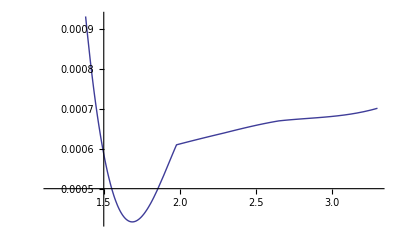

```mathematica
Plot[ssFjk[x][[3,2]],{x,1.15,3.3}]
```

```mathematica
extrap[2]
error[2]
```

{{0.982836,0.00125354,-0.00121075,-0.00425358,0.000517852},{0.00158694,0.988447,-0.163463,0.0151695,0.0000823462},{-0.000650034,-0.0100064,1.2442,-0.029628,0.0028693},{-0.000550155,-0.00255823,-0.0160371,1.15974,-0.00156643},{-0.00045009,-0.00117807,-0.00601955,0.114944,0.89658}}

{{0.00254028,0.00182508,0.00137665,0.00212255,0.000758047},{0.00160874,0.00237448,0.0159111,0.0172772,0.00233058},{0.00180548,0.0015885,0.021753,0.0245587,0.00280035},{0.000956137,0.00151191,0.0180613,0.0204119,0.0025368},{0.000649649,0.00153603,√((0.111639/(0.+nan)^2+0.037005/(-0.00635154 (0.833802 (-2.15338 (-1.48659 (0.00037-nan)-0.879456 (-0.00037+nan))-4.17435 (0.00037-nan))+4.17435 (0.00037-nan))+nan)^2)/(-(0.334124/(0.+nan)^2+0.192367/(-0.00635154 (0.833802 (-2.15338 (-1.48659 (0.00037-nan)-0.879456 (-0.00037+nan))-4.17435 (0.00037-nan))+4.17435 (0.00037-nan))+nan)^2)^2+(0.111639/(0.+nan)^2+0.037005/(-0.00635154 (0.833802 (-2.15338 (-1.48659 (0.00037-nan)-0.879456 (-0.00037+nan))-4.17435 (0.00037-nan))+4.17435 (0.00037-nan))+nan)^2) (1/(0.+nan)^2+1/(-0.00635154 (0.833802 (-2.15338 (-1.48659 (0.00037-nan)-0.879456 (-0.00037+nan))-4.17435 (0.00037-nan))+4.17435 (0.00037-nan))+nan)^2))),0.0116743,0.00478527}}

## Plots

### (27, 1)

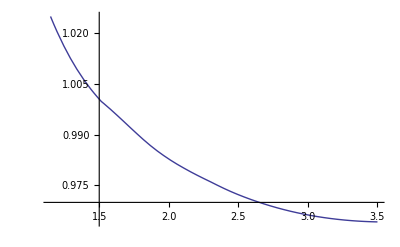

```mathematica
Plot[extrap2[x][[1,1]],{x,1.15,3.5}]
```

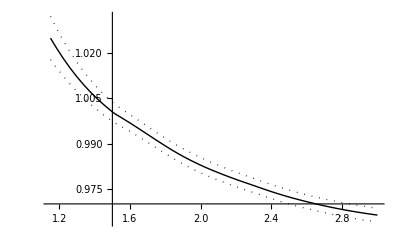

```mathematica
showError[1,1]
```

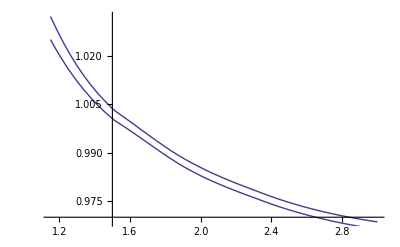

```mathematica
Show[%,%%]
```

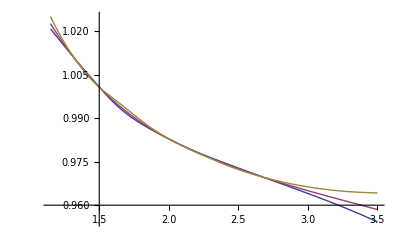

```mathematica
showData[1,1]
```

### (8, 8)

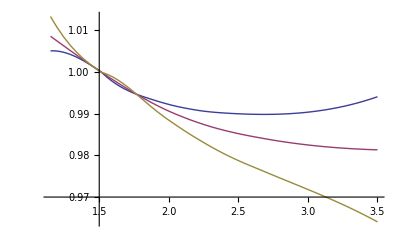

```mathematica
showData[2,2]
```

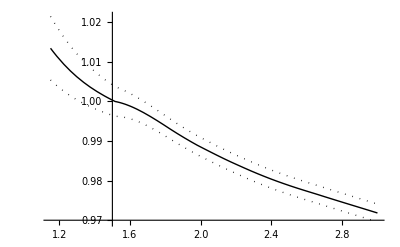

```mathematica
showError[2,2]
```

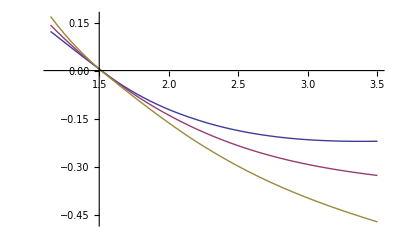

```mathematica
showData[2,3]
```

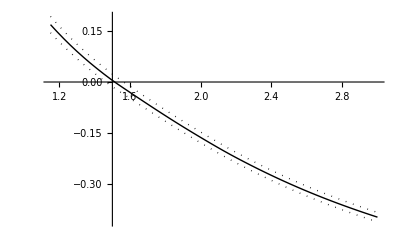

```mathematica
showError[2,3]
```

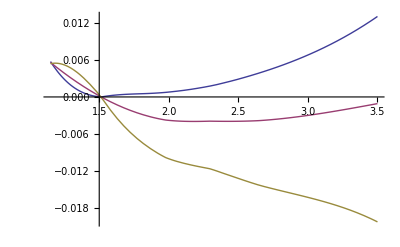

```mathematica
showData[3,2]
```

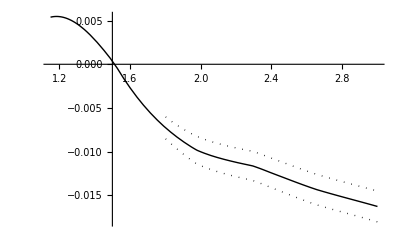

```mathematica
showError[3,2]
```

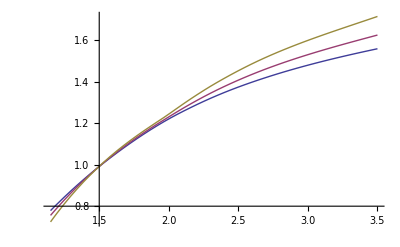

```mathematica
showData[3,3]
```

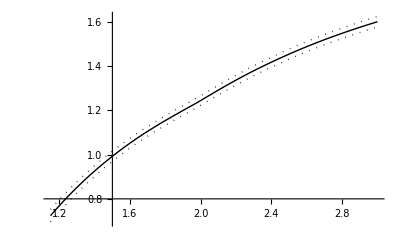

```mathematica
showError[3,3]
```

### (6, OverBar[6])

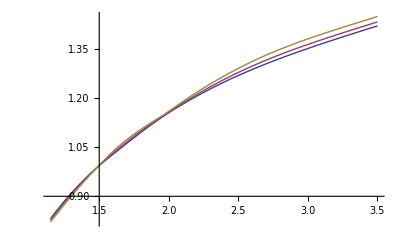

```mathematica
showData[4,4]
```

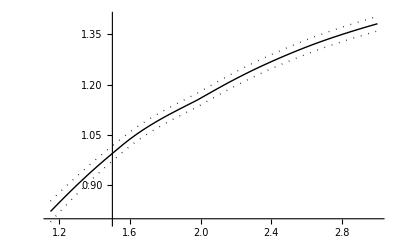

```mathematica
showError[4,4]
```

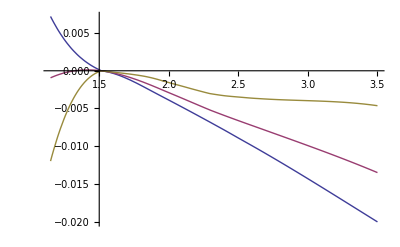

```mathematica
showData[4,5]
```

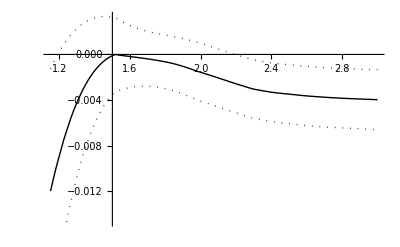

```mathematica
showError[4,5]
```

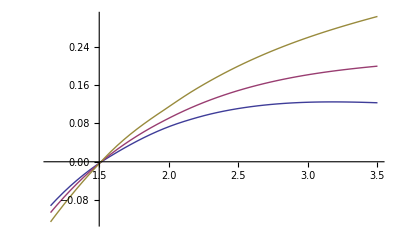

```mathematica
showData[5,4]
```

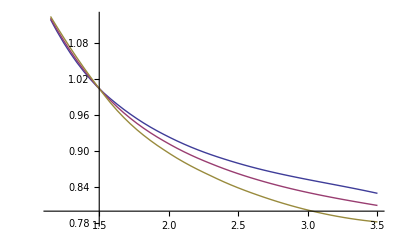

```mathematica
showData[5,5]
```

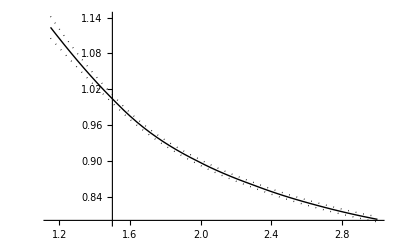

```mathematica
showError[5,5]
```